```mathematica
x1[t_]:= Exp[t]
z1[t_] := NIntegrate[√(1-Exp[2s]), {s, 0, t}]
```

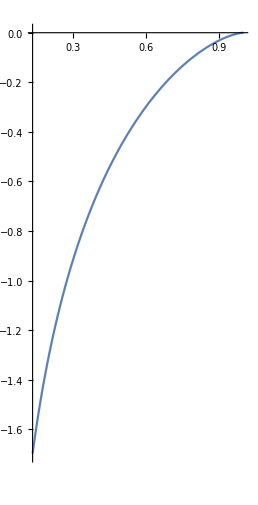

```mathematica
ParametricPlot[{x1[t], z1[t]},{t, -2,0}]
```

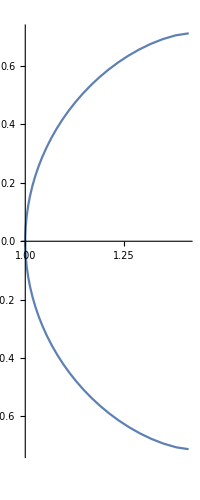

```mathematica
x2[t_]:= Cosh[t]
z2[t_]:= NIntegrate[√(1-Sinh[s]^2), {s, 0, t}]
ParametricPlot[{x2[t], z2[t]}, {t, -100, ArcSinh[1]}]
```

```mathematica
x3[t_]:= Sinh[t]
z3[t_]:= NIntegrate[√(1-Cosh[s]^2), {s, 0, t}]
ParametricPlot[{x3[t],z3[t]}, {t, -10, ArcCosh[1]}]
```

-Graphics-

I cant get this to graph for some reason. I think Something’s wrong. I also am not sure how to show the first curve (graph 1) is the same as the final curve (the tactrix) for question (3).

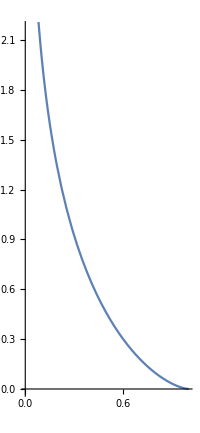

```mathematica
Tx[t_]:= Sin[t]
Tz[t_]:= Cos[t]+Log[Tan[t/2]]
ParametricPlot[{Tx[t],Tz[t]}, {t, π/2, π}]
```